Syntax

```mathematica
a*b+c//f
FullForm[a*(b+c)]

∀_x∃_y x⊗y≻y ∧ m != 0 ⇒ n ⧐̸ m
```

f[a b+c]

Times[a,Plus[b,c]]

∀_x∃_y x⊗y≻y&&m≠0⇒n⧐̸m

Expressions and Brackets

(term)	parentheses for grouping
f[x]	square brackets for functions
{a,b,c}	curly braces for lists
v[[i]]	double brackets for indexing (Part[v, i])

```mathematica
{1,2,3,4,5}
Range[5]
```

{1,2,3,4,5}

{1,2,3,4,5}

Symbolic

```mathematica
x^2+x-4 x^2
```

x-3 x^2

```mathematica
(x+2 y+1) (x-2)^2;
Expand[%]
```

4-3 x^2+x^3+8 y-8 x y+2 x^2 y

```mathematica
1+2 x/.x->3

x->3+y;
x^2-9/.%
```

7

-9+(3+y)^2

```mathematica
x = 7
x+3
x=.
x + 3

t=1+x^2
t/.x->Pi//N
```

7

10

3+x

1+x^2

10.8696

Algebra

```mathematica
Expand[(1+x)^2]
Simplify[x^2+2 x+1]
FullSimplify[Gamma[x] Gamma[1-x]]
```

1+2 x+x^2

(1+x)^2

π Csc[π x]

(1+x)^2

Calculus

```mathematica
(*simple*)
D[x^n,x];
(*partial*)
D[x^2+y^2,x];
(*defaults to partial*)
D[x^2+y[x]^2,x];
(*implicit*)
D[x^2+y^2,x,NonConstants->{y}];
(*gradient*)
D[x^2+y^2,{{x,y}}]
```

{2 x,2 y}

```mathematica
Integrate[1/(x^4-a^4),x]
Integrate[Sin[x^2],x]

Integrate[Exp[-x^2],{x,0,Infinity}]
Integrate[x^x,{x,0,1}]//N

Integrate[x^10 Boole[x^2+y^2≤1],{x,-1,1},{y,-1,1}]
```

-ArcTan[x/a]/(2 a^3)+Log[a-x]/(4 a^3)-Log[a+x]/(4 a^3)

√(π/2) FresnelS[√(2/π) x]

(√π)/2

0.783431

(21 π)/512

```mathematica
Integrate[x^n,x]
Integrate[x^-1,x]
```

x^(1+n)/(1+n)

Log[x]

Differential Equations

```mathematica
DSolve[y'[x]+y[x]==1,y[x],x];
y[x]+2 y'[x]+y[0]/.%

DSolve[y'[x]+y[x]==1,y,x];
y[x]+2 y'[x]+y[0]/.%

y'[x]+y[x]==1/.%%
```

{1+ⅇ^-x C[1]+y[0]+2 y'[x]}

{2+C[1]-ⅇ^-x C[1]}

{True}

```mathematica
DSolve[{y[x]==-z'[x],z[x]==-y'[x]},{y,z},x]
```

{{y→Function[{x},1/2 ⅇ^-x (1+ⅇ^(2 x)) C[1]-1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[2]],z→Function[{x},-1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[1]+1/2 ⅇ^-x (1+ⅇ^(2 x)) C[2]]}}

```mathematica
DSolve[y''[x]-Exp[x] y[x]==0,y[x],x]
DSolve[y''[x]-Cot[x]^2 y[x]==0,y[x],x]

DSolve[y'[x]-y[x]^2==x,y[x],x]//FullSimplify

DSolve[y'[x]-y[x]==UnitStep[x],y[x],x]

DSolve[y'[x]+Clip[x] y[x]==0,y[x],x]
```

{{y[x]→BesselI[0,2 √(ⅇ^x)] C[1]+2 BesselK[0,2 √(ⅇ^x)] C[2]}}

{{y[x]→C[1] (-1+Cos[x]^2)^(1/4) LegendreP[1/2,(√5)/2,Cos[x]]+C[2] (-1+Cos[x]^2)^(1/4) LegendreQ[1/2,(√5)/2,Cos[x]]}}

{{y[x]→(√x (-BesselJ[-2/3,(2 x^(3/2))/3]+BesselJ[2/3,(2 x^(3/2))/3] C[1]))/(BesselJ[1/3,(2 x^(3/2))/3]+BesselJ[-1/3,(2 x^(3/2))/3] C[1])}}

{{y[x]→ⅇ^x C[1]+ⅇ^x (1-ⅇ^-x) UnitStep[x]}}

{{y[x]→ⅇ^Piecewise[{{x, x≤-1}, {-1/2-x^2/2, -1<x≤1}, {-x, True}}] C[1]}}

y^(0,0,1)[x1,x2,x3]+y^(0,1,0)[x1,x2,x3]+y^(1,0,0)[x1,x2,x3]==0

```mathematica
(D[#,x1]+D[#,x2]+D[#,x3])&[y[x1,x2,x3]]==0

(*1d wave equation*)
(c^2 D[#,x,x]-D[#,t,t])&[y[x,t]]==0
```

Plotting

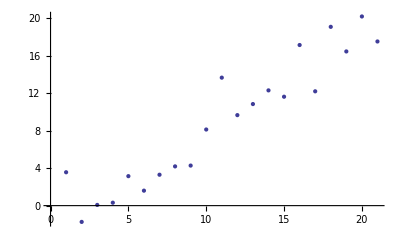

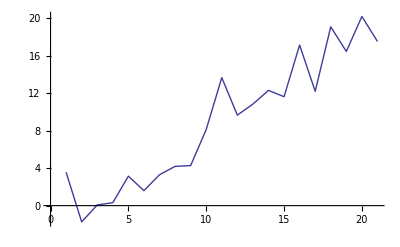

```mathematica
datapts=Table[x+RandomReal[{-4,4}],{x,0,20}];
ListPlot[datapts]
ListLinePlot[datapts]
```

```mathematica
GraphicsGrid[{{Plot3D[Sin[x] Cos[y],{x,0,5},{y,1,10}],Plot3D[Sin[x]*Cos[y],{x,0,5},{y,1,10},ColorFunction->(Hue[#3]&),MeshFunctions->(#3&),Boxed->False,Axes->False]}}]
```

-Graphics-

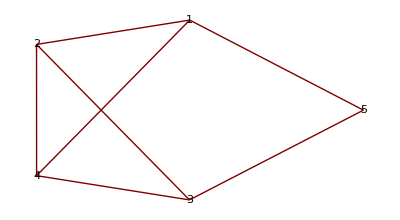

```mathematica
GraphPlot[{1->2,1->4,2->4,3->4,3->2,3->5,5->1},VertexLabeling->True]
```

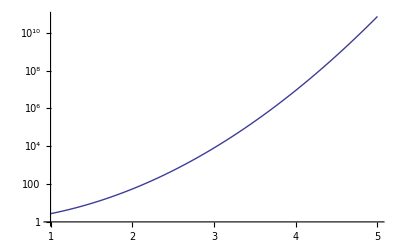

```mathematica
LogPlot[E^x^2,{x,1,5}]
```

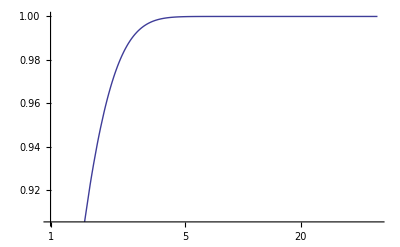

```mathematica
LogLinearPlot[Tanh[x],{x,1,50}]
```

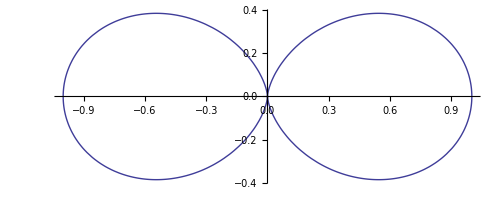

```mathematica
t=.
PolarPlot[Cos[t]^2,{t,0,2 Pi}]
```

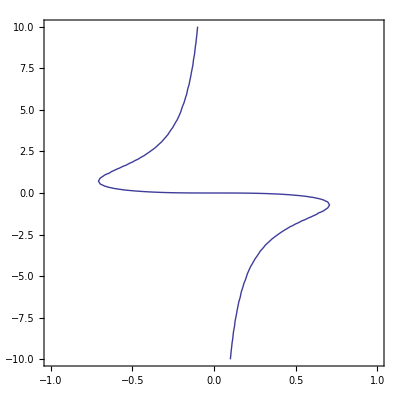

```mathematica
ContourPlot[x^3+x y^2+y==0,{x,-1,1},{y,-10,10}]
```

```mathematica
ParametricPlot3D[{r Cos[t],r Sin[t],Log[r^(1/2)]},{r,0.1,1},{t,0,2 Pi}]
```

-Graphics3D-

{{y→InterpolatingFunction[{{-10.,10.}},<>]}}

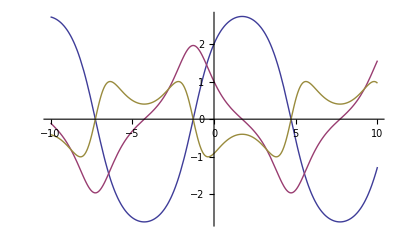

```mathematica
ode1={y''[x]+Sin[y[x]]==0,y[0]==2,y'[0]==1};

sol=NDSolve[ode1,y,{x,-10,10}]

Plot[Evaluate[{y[x],y'[x],y''[x]}/.sol],{x,-10,10}]
```

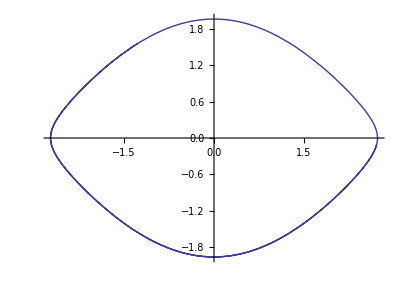

```mathematica
ParametricPlot[Evaluate[{y[x],y'[x]}/.sol],{x,-10,10}]
```

```mathematica
Manipulate[Module[{sol=NDSolve[{y''[x]+Sin[y[x]]==0,y[0]==p[[1]],y'[0]==p[[2]]},y,{x,0,T}]},ParametricPlot[Evaluate[{y[x],y'[x]}/.sol],{x,0,T},PlotRange->{{-4,4},{-3,3}}]],{{p,{2,1}},Locator},{{T,10},0,100}]
```

```mathematica
wws = NDSolve[{D[u[t,x], t,t] == D[u[t,x], x,x] + (1 - u[t, x]^2) (1 + 2 u[t, x]), u[0, x] == E^-x^2, 
Derivative[1,0][u][0, x] == 0, u[t, -10] == u[t, 10]}, 
  u, {t, 0, 10}, {x, -10, 10}]

Plot3D[u[t,x]/.wws,{t,0,10},{x,-10,10}]
```

{{u→InterpolatingFunction[{{0.,10.},{-10.,10.}},<>]}}

-Graphics3D-

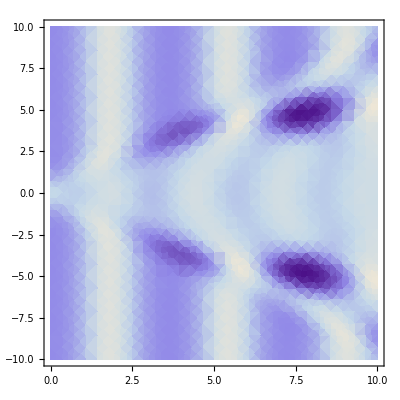

```mathematica
DensityPlot[u[t,x]/.wws,{t,0,10},{x,-10,10}]
```

```mathematica
plots=Table[Plot[u[t,x]/.wws,{x,-10,10},PlotRange->{-2,2}],{t,0,10,.25}];
ListAnimate[plots]
```

```mathematica
bg = NDSolve[{D[u[t], t,t] == (1 - u[t]^2) (1 + 2 u[t]), u[0] == 0, u'[0] == 0}, 
  u, {t, 0, 10}]
plots=Table[Plot[(u[t,x]/.wws)-(u[t]/.bg),{x,-10,10},PlotRange->{-2,2}],{t,0,10,.25}];
ListAnimate[plots]
```

{{u→InterpolatingFunction[{{0.,10.}},<>]}}

```mathematica
Manipulate[n,{n,1,20}]
```

```mathematica
Manipulate[Plot[Sin[n x],{x,0,2 Pi}],{n,1,20,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[a1 Sin[n1 (x+p1)]+a2 Sin[n2 (x+p2)],{x,0,2 Pi},PlotRange->2],{n1,1,20},{a1,0,1},{p1,0,2 Pi},{n2,1,20},{a2,0,1},{p2,0,2 Pi}]
```

```mathematica
Manipulate[Expand[(α+β)^n],{n,1,20,3}]
```

```mathematica
Manipulate[Row[{n,"+",m,"=",n+m}],{n,1/2,1/3,1/144},{m,1/2,1/3,1/144}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,Axis,Top,Bottom}}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Frame->frame,PlotRange->2],{n1,1,20},{n2,1,20},{frame,{True,False}}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,2,1.5,1,0.5,0,-0.5,-1,-1.5,-2}},{filling,-2,2}]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{{n1,1,"Frequency 1"},1,4},{{a1,1,"Amplitude 1"},0,1},{{p1,0,"Phase 1"},0,2 Pi},{{n2,5/4,"Frequency 2"},1,4},{{a2,1,"Amplitude 2"},0,1},{{p2,0,"Phase 2"},0,2 Pi},ControlPlacement->Left]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],Style["Horizontal",12,Bold],{{n1,1,"Frequency"},1,4},{{a1,1,"Amplitude"},0,1},{{p1,0,"Phase"},0,2 Pi},Delimiter,Style["Vertical",12,Bold],{{n2,5/4,"Frequency"},1,4},{{a2,1,"Amplitude"},0,1},{{p2,0,"Phase"},0,2 Pi},ControlPlacement->Left]
```